# Lambdas: clean solutions for H_N

## Finding the solutions of the Bosonic Hamiltonian NxN

```mathematica
matEl[n_,m_,e_,v_]:=Piecewise[{{n*e, n==m}, {Sqrt[m+1]Sqrt[m+2]*(-v), n-m==2}, {Sqrt[m]Sqrt[m-1]*(-v), n-m==-2}}];
bosonMat0[n_,e_,v_]:=Table[Table[matEl[2(i-1),2(j-1),e,v],{j,1,n}],{i,1,n}];
```

```mathematica
qValues=Table[i,{i,0,3,0.05}];
lambdaQ[n_,qs_]:=Table[{qs[[i]],Sort[Eigenvalues[bosonMat0[n,1,qs[[i]]]]]},{i,1,Length[qs]}];
```

```mathematica
plotLambda[id_]:=ListPlot[lambdaQ[10,qValues][[id,2]],Joined->True,PlotStyle->{Red,Thick},PlotMarkers->Automatic];
```

```mathematica
(*Print[lambdaQ[10,qValues][[1,1]]," | ",lambdaQ[10,qValues][[1,2]][[1]]]*)
```

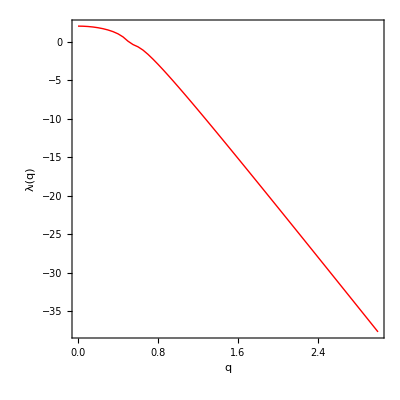

```mathematica
SolutionPos[n_,id_]:=Table[{lambdaQ[n,qValues][[j,1]],lambdaQ[n,qValues][[j,2]][[id]]},{j,1,Length[qValues]}];
plotQEvolution[n_,id_]:=Show[ListLinePlot[SolutionPos[n,id],AspectRatio->1,Frame->True,Axes->False,PlotStyle->{Red,Thick},FrameLabel->{"q","λ_i(q)"}]];
plotQEvolution[10,2]
```

```mathematica
SolutionPos[10,2]
```

{{0.,2.},{0.05,1.98747},{0.1,1.94949},{0.15,1.88485},{0.2,1.79129},{0.25,1.66506},{0.3,1.5},{0.35,1.28538},{0.4,1.0006},{0.45,0.602581},{0.5,0.0438675},{0.55,-0.392414},{0.6,-0.686499},{0.65,-1.11169},{0.7,-1.66309},{0.75,-2.28674},{0.8,-2.95304},{0.85,-3.64761},{0.9,-4.36242},{0.95,-5.09246},{1.,-5.83432},{1.05,-6.58558},{1.1,-7.34447},{1.15,-8.10965},{1.2,-8.88007},{1.25,-9.65493},{1.3,-10.4336},{1.35,-11.2154},{1.4,-12.0001},{1.45,-12.7873},{1.5,-13.5766},{1.55,-14.3678},{1.6,-15.1607},{1.65,-15.9551},{1.7,-16.7508},{1.75,-17.5478},{1.8,-18.3459},{1.85,-19.1449},{1.9,-19.9449},{1.95,-20.7457},{2.,-21.5472},{2.05,-22.3494},{2.1,-23.1523},{2.15,-23.9557},{2.2,-24.7597},{2.25,-25.5642},{2.3,-26.3691},{2.35,-27.1745},{2.4,-27.9803},{2.45,-28.7864},{2.5,-29.5929},{2.55,-30.3997},{2.6,-31.2069},{2.65,-32.0143},{2.7,-32.822},{2.75,-33.6299},{2.8,-34.438},{2.85,-35.2464},{2.9,-36.055},{2.95,-36.8638},{3.,-37.6728}}

```mathematica
Do[Print[lambdaQ[10,1,qValues][[id]]],{id,1,Length[qValues]}]
```

{0.,{0.,2.,4.,6.,8.,10.,12.,14.,16.,18.}}

{0.05,{-0.00250628,1.98747,3.97744,5.96742,7.95739,9.94737,11.9374,13.9283,15.953,18.3467}}

{0.1,{-0.0101021,1.94949,3.90908,5.86867,7.82827,9.7879,11.7495,13.7493,16.0174,19.1505}}

{0.15,{-0.0230304,1.88485,3.79273,5.70061,7.60852,9.51816,11.4583,13.5982,16.3072,20.1544}}

{0.2,{-0.0417424,1.79129,3.62432,5.45737,7.29144,9.14565,11.1448,13.5735,16.7586,21.2548}}

{0.25,{-0.0669873,1.66506,3.39712,5.12962,6.87338,8.71656,10.8959,13.671,17.3091,22.4094}}

{0.3,{-0.1,1.5,3.10014,4.70556,6.3743,8.30523,10.7379,13.8567,17.9223,23.5979}}

{0.35,{-0.142929,1.28538,2.71572,4.18332,5.85249,7.95807,10.6575,14.1036,18.5777,24.8092}}

{0.4,{-0.199998,1.0006,2.22201,3.6,5.36946,7.6795,10.635,14.3937,19.263,26.0367}}

{0.45,{-0.281954,0.602581,1.62625,3.03006,4.94875,7.45698,10.6555,14.7155,19.9701,27.2763}}

{0.5,{-0.439808,0.0438675,1.02294,2.52251,4.58491,7.27744,10.7081,15.0612,20.6939,28.525}}

{0.55,{-1.01405,-0.392414,0.507922,2.07911,4.26613,7.13093,10.7856,15.4254,21.4306,29.7808}}

{0.6,{-1.99759,-0.686499,0.0969997,1.68744,3.98256,7.01029,10.8827,15.8042,22.1776,31.0423}}

{0.65,{-3.10094,-1.11169,-0.193895,1.33755,3.72698,6.91028,10.9954,16.1949,22.933,32.3084}}

{0.7,{-4.26061,-1.66309,-0.411324,1.02409,3.4941,6.82706,11.121,16.5952,23.6952,33.5783}}

{0.75,{-5.45369,-2.28674,-0.618718,0.746083,3.28003,6.7577,11.2572,17.0036,24.4631,34.8514}}

{0.8,{-6.6688,-2.95304,-0.848449,0.504554,3.08181,6.69992,11.4022,17.4188,25.2358,36.1272}}

{0.85,{-7.89941,-3.64761,-1.11289,0.298485,2.89718,6.65196,11.5548,17.8397,26.0125,37.4053}}

{0.9,{-9.14143,-4.36242,-1.41296,0.122636,2.72443,6.61239,11.7138,18.2655,26.7928,38.6853}}

{0.95,{-10.3921,-5.09246,-1.74373,-0.0309516,2.56229,6.58006,11.8784,18.6955,27.576,39.967}}

{1.,{-11.6496,-5.83432,-2.09878,-0.170188,2.40978,6.55402,12.0478,19.1292,28.3619,41.2502}}

{1.05,{-12.9125,-6.58558,-2.47248,-0.301406,2.26618,6.53349,12.2214,19.5661,29.1501,42.5347}}

{1.1,{-14.1798,-7.34447,-2.86053,-0.429167,2.13094,6.51782,12.3987,20.0059,29.9403,43.8203}}

{1.15,{-15.4507,-8.10965,-3.25981,-0.556604,2.0036,6.50647,12.5793,20.4481,30.7324,45.1069}}

{1.2,{-16.7246,-8.88007,-3.66803,-0.685819,1.88377,6.49895,12.7628,20.8926,31.526,46.3944}}

{1.25,{-18.0011,-9.65493,-4.08353,-0.818189,1.77107,6.49489,12.9489,21.3391,32.321,47.6828}}

{1.3,{-19.2798,-10.4336,-4.50505,-0.954583,1.66513,6.49392,13.1374,21.7874,33.1173,48.9718}}

{1.35,{-20.5604,-11.2154,-4.93162,-1.0955,1.56555,6.49576,13.328,22.2373,33.9148,50.2615}}

{1.4,{-21.8426,-12.0001,-5.36248,-1.24118,1.47193,6.50015,13.5204,22.6886,34.7134,51.5518}}

{1.45,{-23.1262,-12.7873,-5.79704,-1.39166,1.38382,6.50685,13.7146,23.1413,35.5128,52.8427}}

{1.5,{-24.411,-13.5766,-6.2348,-1.54686,1.30077,6.51569,13.9104,23.5952,36.3132,54.134}}

{1.55,{-25.6969,-14.3678,-6.67536,-1.70661,1.22236,6.52647,14.1076,24.0502,37.1143,55.4257}}

{1.6,{-26.9839,-15.1607,-7.11839,-1.87066,1.14813,6.53905,14.3061,24.5062,37.9162,56.7179}}

{1.65,{-28.2717,-15.9551,-7.5636,-2.03874,1.07768,6.55329,14.5058,24.9631,38.7187,58.0105}}

{1.7,{-29.5602,-16.7508,-8.01077,-2.21057,1.0106,6.56907,14.7067,25.4208,39.5218,59.3034}}

{1.75,{-30.8495,-17.5478,-8.45967,-2.38587,0.946534,6.58627,14.9085,25.8794,40.3255,60.5966}}

{1.8,{-32.1394,-18.3459,-8.91015,-2.56435,0.885134,6.60481,15.1113,26.3386,41.1297,61.8901}}

{1.85,{-33.4299,-19.1449,-9.36204,-2.74574,0.826095,6.62459,15.315,26.7986,41.9344,63.1839}}

{1.9,{-34.7209,-19.9449,-9.81522,-2.92981,0.769139,6.64552,15.5195,27.2591,42.7396,64.4779}}

{1.95,{-36.0123,-20.7457,-10.2696,-3.11632,0.714018,6.66755,15.7248,27.7202,43.5451,65.7722}}

{2.,{-37.3042,-21.5472,-10.725,-3.30505,0.660508,6.6906,15.9307,28.1819,44.3511,67.0667}}

{2.05,{-38.5965,-22.3494,-11.1814,-3.49583,0.608413,6.71461,16.1373,28.6441,45.1574,68.3614}}

{2.1,{-39.8892,-23.1523,-11.6386,-3.68846,0.557557,6.73952,16.3445,29.1067,45.964,69.6562}}

{2.15,{-41.1822,-23.9557,-12.0967,-3.8828,0.507785,6.76529,16.5523,29.5698,46.771,70.9513}}

{2.2,{-42.4755,-24.7597,-12.5556,-4.0787,0.458962,6.79187,16.7607,30.0333,47.5782,72.2465}}

{2.25,{-43.7691,-25.5642,-13.0152,-4.27603,0.410966,6.81922,16.9695,30.4971,48.3858,73.5419}}

{2.3,{-45.063,-26.3691,-13.4754,-4.47467,0.363693,6.84729,17.1788,30.9613,49.1936,74.8375}}

{2.35,{-46.3571,-27.1745,-13.9362,-4.67452,0.317047,6.87605,17.3886,31.4259,50.0016,76.1331}}

{2.4,{-47.6514,-27.9803,-14.3976,-4.87549,0.270948,6.90547,17.5988,31.8908,50.8099,77.429}}

{2.45,{-48.946,-28.7864,-14.8595,-5.07749,0.225322,6.93551,17.8093,32.356,51.6183,78.7249}}

{2.5,{-50.2408,-29.5929,-15.3218,-5.28044,0.180106,6.96615,18.0203,32.8215,52.427,80.0209}}

{2.55,{-51.5357,-30.3997,-15.7847,-5.48427,0.135243,6.99735,18.2316,33.2872,53.2359,81.3171}}

{2.6,{-52.8308,-31.2069,-16.2479,-5.68892,0.0906832,7.02909,18.4432,33.7532,54.045,82.6134}}

{2.65,{-54.1261,-32.0143,-16.7116,-5.89432,0.0463832,7.06135,18.6552,34.2195,54.8542,83.9097}}

{2.7,{-55.4215,-32.822,-17.1756,-6.10044,0.00230411,7.0941,18.8674,34.6859,55.6636,85.2062}}

{2.75,{-56.7171,-33.6299,-17.64,-6.30721,-0.0415884,7.12733,19.08,35.1526,56.4732,86.5027}}

{2.8,{-58.0129,-34.438,-18.1048,-6.5146,-0.0853246,7.161,19.2928,35.6195,57.2829,87.7993}}

{2.85,{-59.3087,-35.2464,-18.5698,-6.72256,-0.128931,7.19511,19.5059,36.0866,58.0928,89.0961}}

{2.9,{-60.6047,-36.055,-19.0351,-6.93106,-0.172432,7.22964,19.7192,36.5539,58.9028,90.3928}}

{2.95,{-61.9008,-36.8638,-19.5007,-7.14007,-0.215847,7.26456,19.9327,37.0214,59.7129,91.6897}}

{3.,{-63.1969,-37.6728,-19.9666,-7.34955,-0.259196,7.29987,20.1465,37.489,60.5231,92.9866}}